# Quiz 2

Each task is worth 1 point unless otherwise stated. You can score a maximum of 20 points.

## Task 1

a)  Define a function A(n, m) that takes natural numbers n and m and returns a matrix of dimensions n × m, where each element in the matrix is the product of the column index and the row index (starting from 1).

```mathematica
A[n_,m_]:=Table[i+j,{i,1 ,n},{j, 1, m}]
```

b) Show that A is a symmetric matrix.

```mathematica
tf = isSymmetric(A)
```

A isSymmetric

c) Calculate the eigenvalues and eigenvectors of the matrix A(10, 10).

```mathematica
matrika=A[10,10];
Eigenvalues[matrika] 
Eigenvectors[matrika]
```

{5 (11+√154),5 (11-√154),0,0,0,0,0,0,0,0}

{{-(-150258053-12108139 √154)/(337954529+27233152 √154),(3 (57037739+4596232 √154))/(337954529+27233152 √154),-(-191968381-15469253 √154)/(337954529+27233152 √154),(5 (42564709+3429962 √154))/(337954529+27233152 √154),(27 (8654767+697421 √154))/(337954529+27233152 √154),-(-254533873-20510924 √154)/(337954529+27233152 √154),-(-275389037-22191481 √154)/(337954529+27233152 √154),(3 (98748067+7957346 √154))/(337954529+27233152 √154),(5 (63419873+5110519 √154))/(337954529+27233152 √154),1},{-(150258053-12108139 √154)/(-337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),1},{8,-9,0,0,0,0,0,0,0,1},{7,-8,0,0,0,0,0,0,1,0},{6,-7,0,0,0,0,0,1,0,0},{5,-6,0,0,0,0,1,0,0,0},{4,-5,0,0,0,1,0,0,0,0},{3,-4,0,0,1,0,0,0,0,0},{2,-3,0,1,0,0,0,0,0,0},{1,-2,1,0,0,0,0,0,0,0}}

d) Calculate the characteristic polynomial of the matrix A(10, 10).

```mathematica
CharacteristicPolynomial[matrika,λ]
```

-825 λ^8-110 λ^9+λ^10

e) Diagonalize the matrix A(10, 10). Determine the corresponding diagonal matrix G, the transition matrix P, and the inverse P⁻.b9.

```mathematica
P=Transpose[Eigenvectors[A[10,10]]]; 
G=DiagonalMatrix[Eigenvalues[A[10,10]]];
R = Inverse[P];
Print[P, G, R]
```

{{-(-150258053-12108139 √154)/(337954529+27233152 √154),-(150258053-12108139 √154)/(-337954529+27233152 √154),8,7,6,5,4,3,2,1},{(3 (57037739+4596232 √154))/(337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-9,-8,-7,-6,-5,-4,-3,-2},{-(-191968381-15469253 √154)/(337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),0,0,0,0,0,0,0,1},{(5 (42564709+3429962 √154))/(337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),0,0,0,0,0,0,1,0},{(27 (8654767+697421 √154))/(337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),0,0,0,0,0,1,0,0},{-(-254533873-20510924 √154)/(337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),0,0,0,0,1,0,0,0},{-(-275389037-22191481 √154)/(337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),0,0,0,1,0,0,0,0},{(3 (98748067+7957346 √154))/(337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),0,0,1,0,0,0,0,0},{(5 (63419873+5110519 √154))/(337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}}{{5 (11+√154),0,0,0,0,0,0,0,0,0},{0,5 (11-√154),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}{{(9-9663743364/(-337954529+27233152 √154)+(778726632 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8-7560634983/(-337954529+27233152 √154)+(609253329 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7-5457526602/(-337954529+27233152 √154)+(439780026 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(6-3354418221/(-337954529+27233152 √154)+(270306723 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(5-1251309840/(-337954529+27233152 √154)+(100833420 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(4+851798541/(-337954529+27233152 √154)-(68639883 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(3+2954906922/(-337954529+27233152 √154)-(238113186 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(2+5058015303/(-337954529+27233152 √154)-(407586489 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(1+7161123684/(-337954529+27233152 √154)-(577059792 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))},{(-9-9663743364/(337954529+27233152 √154)-(778726632 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-8-7560634983/(337954529+27233152 √154)-(609253329 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-7-5457526602/(337954529+27233152 √154)-(439780026 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-6-3354418221/(337954529+27233152 √154)-(270306723 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-5-1251309840/(337954529+27233152 √154)-(100833420 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-4+851798541/(337954529+27233152 √154)+(68639883 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-3+2954906922/(337954529+27233152 √154)+(238113186 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2+5058015303/(337954529+27233152 √154)+(407586489 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1+7161123684/(337954529+27233152 √154)+(577059792 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))},{(9663743364/(-337954529+27233152 √154)-(778726632 √154)/(-337954529+27233152 √154)+9663743364/(337954529+27233152 √154)+(778726632 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7560634983/(-337954529+27233152 √154)-(609253329 √154)/(-337954529+27233152 √154)+7560634983/(337954529+27233152 √154)+(609253329 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(5457526602/(-337954529+27233152 √154)-(439780026 √154)/(-337954529+27233152 √154)+5457526602/(337954529+27233152 √154)+(439780026 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(3354418221/(-337954529+27233152 √154)-(270306723 √154)/(-337954529+27233152 √154)+3354418221/(337954529+27233152 √154)+(270306723 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(1251309840/(-337954529+27233152 √154)-(100833420 √154)/(-337954529+27233152 √154)+1251309840/(337954529+27233152 √154)+(100833420 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-851798541/(-337954529+27233152 √154)+(68639883 √154)/(-337954529+27233152 √154)-851798541/(337954529+27233152 √154)-(68639883 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2954906922/(-337954529+27233152 √154)+(238113186 √154)/(-337954529+27233152 √154)-2954906922/(337954529+27233152 √154)-(238113186 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-5058015303/(-337954529+27233152 √154)+(407586489 √154)/(-337954529+27233152 √154)-5058015303/(337954529+27233152 √154)-(407586489 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-7161123684/(-337954529+27233152 √154)+(577059792 √154)/(-337954529+27233152 √154)-7161123684/(337954529+27233152 √154)-(577059792 √154)/(337954529+27233152 √154))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),-((1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))))},{(-2853894285/(-337954529+27233152 √154)+(229973355 √154)/(-337954529+27233152 √154)-2853894285/(337954529+27233152 √154)-(229973355 √154)/(337954529+27233152 √154)-(303118200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2536794920/(-337954529+27233152 √154)+(204420760 √154)/(-337954529+27233152 √154)-2536794920/(337954529+27233152 √154)-(204420760 √154)/(337954529+27233152 √154)-(173210400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2219695555/(-337954529+27233152 √154)+(178868165 √154)/(-337954529+27233152 √154)-2219695555/(337954529+27233152 √154)-(178868165 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1902596190/(-337954529+27233152 √154)+(153315570 √154)/(-337954529+27233152 √154)-1902596190/(337954529+27233152 √154)-(153315570 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1585496825/(-337954529+27233152 √154)+(127762975 √154)/(-337954529+27233152 √154)-1585496825/(337954529+27233152 √154)-(127762975 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1268397460/(-337954529+27233152 √154)+(102210380 √154)/(-337954529+27233152 √154)-1268397460/(337954529+27233152 √154)-(102210380 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-951298095/(-337954529+27233152 √154)+(76657785 √154)/(-337954529+27233152 √154)-951298095/(337954529+27233152 √154)-(76657785 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-634198730/(-337954529+27233152 √154)+(51105190 √154)/(-337954529+27233152 √154)-634198730/(337954529+27233152 √154)-(51105190 √154)/(337954529+27233152 √154)+(606236400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8947132700/(-337954529+27233152 √154)-(720980500 √154)/(-337954529+27233152 √154)+8947132700/(337954529+27233152 √154)+(720980500 √154)/(337954529+27233152 √154)-(1212472800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(866052000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2666197809/(-337954529+27233152 √154)+(214848342 √154)/(-337954529+27233152 √154)-2666197809/(337954529+27233152 √154)-(214848342 √154)/(337954529+27233152 √154)-(173210400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2369953608/(-337954529+27233152 √154)+(190976304 √154)/(-337954529+27233152 √154)-2369953608/(337954529+27233152 √154)-(190976304 √154)/(337954529+27233152 √154)-(75779550 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2073709407/(-337954529+27233152 √154)+(167104266 √154)/(-337954529+27233152 √154)-2073709407/(337954529+27233152 √154)-(167104266 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1777465206/(-337954529+27233152 √154)+(143232228 √154)/(-337954529+27233152 √154)-1777465206/(337954529+27233152 √154)-(143232228 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1481221005/(-337954529+27233152 √154)+(119360190 √154)/(-337954529+27233152 √154)-1481221005/(337954529+27233152 √154)-(119360190 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1184976804/(-337954529+27233152 √154)+(95488152 √154)/(-337954529+27233152 √154)-1184976804/(337954529+27233152 √154)-(95488152 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-888732603/(-337954529+27233152 √154)+(71616114 √154)/(-337954529+27233152 √154)-888732603/(337954529+27233152 √154)-(71616114 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8671743663/(-337954529+27233152 √154)-(698789019 √154)/(-337954529+27233152 √154)+8671743663/(337954529+27233152 √154)+(698789019 √154)/(337954529+27233152 √154)-(1439811450 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-296244201/(-337954529+27233152 √154)+(23872038 √154)/(-337954529+27233152 √154)-296244201/(337954529+27233152 √154)-(23872038 √154)/(337954529+27233152 √154)+(606236400 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(703667250 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2478501333/(-337954529+27233152 √154)+(199723329 √154)/(-337954529+27233152 √154)-2478501333/(337954529+27233152 √154)-(199723329 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2203112296/(-337954529+27233152 √154)+(177531848 √154)/(-337954529+27233152 √154)-2203112296/(337954529+27233152 √154)-(177531848 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1927723259/(-337954529+27233152 √154)+(155340367 √154)/(-337954529+27233152 √154)-1927723259/(337954529+27233152 √154)-(155340367 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1652334222/(-337954529+27233152 √154)+(133148886 √154)/(-337954529+27233152 √154)-1652334222/(337954529+27233152 √154)-(133148886 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1376945185/(-337954529+27233152 √154)+(110957405 √154)/(-337954529+27233152 √154)-1376945185/(337954529+27233152 √154)-(110957405 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1101556148/(-337954529+27233152 √154)+(88765924 √154)/(-337954529+27233152 √154)-1101556148/(337954529+27233152 √154)-(88765924 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8438064954/(-337954529+27233152 √154)-(679958652 √154)/(-337954529+27233152 √154)+8438064954/(337954529+27233152 √154)+(679958652 √154)/(337954529+27233152 √154)-(1602196200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-550778074/(-337954529+27233152 √154)+(44382962 √154)/(-337954529+27233152 √154)-550778074/(337954529+27233152 √154)-(44382962 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-275389037/(-337954529+27233152 √154)+(22191481 √154)/(-337954529+27233152 √154)-275389037/(337954529+27233152 √154)-(22191481 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(541282500 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2290804857/(-337954529+27233152 √154)+(184598316 √154)/(-337954529+27233152 √154)-2290804857/(337954529+27233152 √154)-(184598316 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-2036270984/(-337954529+27233152 √154)+(164087392 √154)/(-337954529+27233152 √154)-2036270984/(337954529+27233152 √154)-(164087392 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1781737111/(-337954529+27233152 √154)+(143576468 √154)/(-337954529+27233152 √154)-1781737111/(337954529+27233152 √154)-(143576468 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1527203238/(-337954529+27233152 √154)+(123065544 √154)/(-337954529+27233152 √154)-1527203238/(337954529+27233152 √154)-(123065544 √154)/(337954529+27233152 √154)+(184036050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1272669365/(-337954529+27233152 √154)+(102554620 √154)/(-337954529+27233152 √154)-1272669365/(337954529+27233152 √154)-(102554620 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8246096573/(-337954529+27233152 √154)-(664489399 √154)/(-337954529+27233152 √154)+8246096573/(337954529+27233152 √154)+(664489399 √154)/(337954529+27233152 √154)-(1699627050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-763601619/(-337954529+27233152 √154)+(61532772 √154)/(-337954529+27233152 √154)-763601619/(337954529+27233152 √154)-(61532772 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-509067746/(-337954529+27233152 √154)+(41021848 √154)/(-337954529+27233152 √154)-509067746/(337954529+27233152 √154)-(41021848 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-254533873/(-337954529+27233152 √154)+(20510924 √154)/(-337954529+27233152 √154)-254533873/(337954529+27233152 √154)-(20510924 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(378897750 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-2103108381/(-337954529+27233152 √154)+(169473303 √154)/(-337954529+27233152 √154)-2103108381/(337954529+27233152 √154)-(169473303 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1869429672/(-337954529+27233152 √154)+(150642936 √154)/(-337954529+27233152 √154)-1869429672/(337954529+27233152 √154)-(150642936 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1635750963/(-337954529+27233152 √154)+(131812569 √154)/(-337954529+27233152 √154)-1635750963/(337954529+27233152 √154)-(131812569 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1402072254/(-337954529+27233152 √154)+(112982202 √154)/(-337954529+27233152 √154)-1402072254/(337954529+27233152 √154)-(112982202 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(8095838520/(-337954529+27233152 √154)-(652381260 √154)/(-337954529+27233152 √154)+8095838520/(337954529+27233152 √154)+(652381260 √154)/(337954529+27233152 √154)-(1732104000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-934714836/(-337954529+27233152 √154)+(75321468 √154)/(-337954529+27233152 √154)-934714836/(337954529+27233152 √154)-(75321468 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-701036127/(-337954529+27233152 √154)+(56491101 √154)/(-337954529+27233152 √154)-701036127/(337954529+27233152 √154)-(56491101 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-467357418/(-337954529+27233152 √154)+(37660734 √154)/(-337954529+27233152 √154)-467357418/(337954529+27233152 √154)-(37660734 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-233678709/(-337954529+27233152 √154)+(18830367 √154)/(-337954529+27233152 √154)-233678709/(337954529+27233152 √154)-(18830367 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-1915411905/(-337954529+27233152 √154)+(154348290 √154)/(-337954529+27233152 √154)-1915411905/(337954529+27233152 √154)-(154348290 √154)/(337954529+27233152 √154)+(346420800 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1702588360/(-337954529+27233152 √154)+(137198480 √154)/(-337954529+27233152 √154)-1702588360/(337954529+27233152 √154)-(137198480 √154)/(337954529+27233152 √154)+(313943850 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1489764815/(-337954529+27233152 √154)+(120048670 √154)/(-337954529+27233152 √154)-1489764815/(337954529+27233152 √154)-(120048670 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7987290795/(-337954529+27233152 √154)-(643634235 √154)/(-337954529+27233152 √154)+7987290795/(337954529+27233152 √154)+(643634235 √154)/(337954529+27233152 √154)-(1699627050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1064117725/(-337954529+27233152 √154)+(85749050 √154)/(-337954529+27233152 √154)-1064117725/(337954529+27233152 √154)-(85749050 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-851294180/(-337954529+27233152 √154)+(68599240 √154)/(-337954529+27233152 √154)-851294180/(337954529+27233152 √154)-(68599240 √154)/(337954529+27233152 √154)+(184036050 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-638470635/(-337954529+27233152 √154)+(51449430 √154)/(-337954529+27233152 √154)-638470635/(337954529+27233152 √154)-(51449430 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-425647090/(-337954529+27233152 √154)+(34299620 √154)/(-337954529+27233152 √154)-425647090/(337954529+27233152 √154)-(34299620 √154)/(337954529+27233152 √154)+(119082150 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-212823545/(-337954529+27233152 √154)+(17149810 √154)/(-337954529+27233152 √154)-212823545/(337954529+27233152 √154)-(17149810 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(54128250 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))))},{(-1727715429/(-337954529+27233152 √154)+(139223277 √154)/(-337954529+27233152 √154)-1727715429/(337954529+27233152 √154)-(139223277 √154)/(337954529+27233152 √154)+(476328600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1535747048/(-337954529+27233152 √154)+(123754024 √154)/(-337954529+27233152 √154)-1535747048/(337954529+27233152 √154)-(123754024 √154)/(337954529+27233152 √154)+(411374700 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(7920453398/(-337954529+27233152 √154)-(638248324 √154)/(-337954529+27233152 √154)+7920453398/(337954529+27233152 √154)+(638248324 √154)/(337954529+27233152 √154)-(1602196200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-1151810286/(-337954529+27233152 √154)+(92815518 √154)/(-337954529+27233152 √154)-1151810286/(337954529+27233152 √154)-(92815518 √154)/(337954529+27233152 √154)+(281466900 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-959841905/(-337954529+27233152 √154)+(77346265 √154)/(-337954529+27233152 √154)-959841905/(337954529+27233152 √154)-(77346265 √154)/(337954529+27233152 √154)+(216513000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-767873524/(-337954529+27233152 √154)+(61877012 √154)/(-337954529+27233152 √154)-767873524/(337954529+27233152 √154)-(61877012 √154)/(337954529+27233152 √154)+(151559100 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-575905143/(-337954529+27233152 √154)+(46407759 √154)/(-337954529+27233152 √154)-575905143/(337954529+27233152 √154)-(46407759 √154)/(337954529+27233152 √154)+(86605200 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-383936762/(-337954529+27233152 √154)+(30938506 √154)/(-337954529+27233152 √154)-383936762/(337954529+27233152 √154)-(30938506 √154)/(337954529+27233152 √154)+(21651300 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),(-191968381/(-337954529+27233152 √154)+(15469253 √154)/(-337954529+27233152 √154)-191968381/(337954529+27233152 √154)-(15469253 √154)/(337954529+27233152 √154)-(43302600 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))/(9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154))),-((108256500 √154)/((-337954529+27233152 √154) (337954529+27233152 √154) (9264232065/(-337954529+27233152 √154)-(746533095 √154)/(-337954529+27233152 √154)+9264232065/(337954529+27233152 √154)+(746533095 √154)/(337954529+27233152 √154)-(1948617000 √154)/((-337954529+27233152 √154) (337954529+27233152 √154)))))}}

f) (2 points) Solve the matrix equation:
    A(10,10)·X + P·X == G·X + I

```mathematica
X=LinearSolve[A[10,10]+P-G, IdentityMatrix[10]]
A[10,10].X+P.X==G.X+IdentityMatrix[10]//Simplify
```

Thread::tdlen: Objects of unequal length in {{2,3,4},{3,4,5},{4,5,6}}+{{«1»},{«1»},«7»,{1,1,1,0,0,0,0,0,0,0}}+{{-5 (11+√154),0,0,0,0,0,0,0,0,0},{0,-5 (11-√154),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}} cannot be combined.

LinearSolve[{{2,3,4},{3,4,5},{4,5,6}}+{{-5 (11+√154),0,0,0,0,0,0,0,0,0},{0,-5 (11-√154),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}+{{-(-150258053-12108139 √154)/(337954529+27233152 √154),-(150258053-12108139 √154)/(-337954529+27233152 √154),8,7,6,5,4,3,2,1},{(3 (57037739+4596232 √154))/(337954529+27233152 √154),(3 (-57037739+4596232 √154))/(-337954529+27233152 √154),-9,-8,-7,-6,-5,-4,-3,-2},{-(-191968381-15469253 √154)/(337954529+27233152 √154),-(191968381-15469253 √154)/(-337954529+27233152 √154),0,0,0,0,0,0,0,1},{(5 (42564709+3429962 √154))/(337954529+27233152 √154),(5 (-42564709+3429962 √154))/(-337954529+27233152 √154),0,0,0,0,0,0,1,0},{(27 (8654767+697421 √154))/(337954529+27233152 √154),(27 (-8654767+697421 √154))/(-337954529+27233152 √154),0,0,0,0,0,1,0,0},{-(-254533873-20510924 √154)/(337954529+27233152 √154),-(254533873-20510924 √154)/(-337954529+27233152 √154),0,0,0,0,1,0,0,0},{-(-275389037-22191481 √154)/(337954529+27233152 √154),-(275389037-22191481 √154)/(-337954529+27233152 √154),0,0,0,1,0,0,0,0},{(3 (98748067+7957346 √154))/(337954529+27233152 √154),(3 (-98748067+7957346 √154))/(-337954529+27233152 √154),0,0,1,0,0,0,0,0},{(5 (63419873+5110519 √154))/(337954529+27233152 √154),(5 (-63419873+5110519 √154))/(-337954529+27233152 √154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}]

{{2,3,4},{3,4,5},{4,5,6}}.LinearSolve[{{2,3,4},{3,4,5},{4,5,6}}+{{-2/41 (1137+101 √154),1/41 (-19-3 √154),8,7,6,5,4,3,2,1},{1/123 (-37+8 √154),1/123 (-6802+607 √154),-9,-8,-7,-6,-5,-4,-3,-2},{1/123 (-17+7 √154),1/123 (-17-7 √154),0,0,0,0,0,0,0,1},{1/41 (1+2 √154),1/41 (1-2 √154),0,0,0,0,0,0,1,0},{1/123 (23+5 √154),1/123 (23-5 √154),0,0,0,0,0,1,0,0},{1/123 (43+4 √154),1/123 (43-4 √154),0,0,0,0,1,0,0,0},{1/41 (21+√154),1/41 (21-√154),0,0,0,1,0,0,0,0},{1/123 (83+2 √154),1/123 (83-2 √154),0,0,1,0,0,0,0,0},{1/123 (103+√154),1/123 (103-√154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}]+{{1/41 (-19+3 √154),1/41 (-19-3 √154),8,7,6,5,4,3,2,1},{1/123 (-37+8 √154),1/123 (-37-8 √154),-9,-8,-7,-6,-5,-4,-3,-2},{1/123 (-17+7 √154),1/123 (-17-7 √154),0,0,0,0,0,0,0,1},{1/41 (1+2 √154),1/41 (1-2 √154),0,0,0,0,0,0,1,0},{1/123 (23+5 √154),1/123 (23-5 √154),0,0,0,0,0,1,0,0},{1/123 (43+4 √154),1/123 (43-4 √154),0,0,0,0,1,0,0,0},{1/41 (21+√154),1/41 (21-√154),0,0,0,1,0,0,0,0},{1/123 (83+2 √154),1/123 (83-2 √154),0,0,1,0,0,0,0,0},{1/123 (103+√154),1/123 (103-√154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}}.LinearSolve[{{2,3,4},{3,4,5},{4,5,6}}+{{-2/41 (1137+101 √154),1/41 (-19-3 √154),8,7,6,5,4,3,2,1},{1/123 (-37+8 √154),1/123 (-6802+607 √154),-9,-8,-7,-6,-5,-4,-3,-2},{1/123 (-17+7 √154),1/123 (-17-7 √154),0,0,0,0,0,0,0,1},{1/41 (1+2 √154),1/41 (1-2 √154),0,0,0,0,0,0,1,0},{1/123 (23+5 √154),1/123 (23-5 √154),0,0,0,0,0,1,0,0},{1/123 (43+4 √154),1/123 (43-4 √154),0,0,0,0,1,0,0,0},{1/41 (21+√154),1/41 (21-√154),0,0,0,1,0,0,0,0},{1/123 (83+2 √154),1/123 (83-2 √154),0,0,1,0,0,0,0,0},{1/123 (103+√154),1/123 (103-√154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}]=={{5 (11+√154),0,0,0,0,0,0,0,0,0},{0,55-5 √154,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}.LinearSolve[{{2,3,4},{3,4,5},{4,5,6}}+{{-2/41 (1137+101 √154),1/41 (-19-3 √154),8,7,6,5,4,3,2,1},{1/123 (-37+8 √154),1/123 (-6802+607 √154),-9,-8,-7,-6,-5,-4,-3,-2},{1/123 (-17+7 √154),1/123 (-17-7 √154),0,0,0,0,0,0,0,1},{1/41 (1+2 √154),1/41 (1-2 √154),0,0,0,0,0,0,1,0},{1/123 (23+5 √154),1/123 (23-5 √154),0,0,0,0,0,1,0,0},{1/123 (43+4 √154),1/123 (43-4 √154),0,0,0,0,1,0,0,0},{1/41 (21+√154),1/41 (21-√154),0,0,0,1,0,0,0,0},{1/123 (83+2 √154),1/123 (83-2 √154),0,0,1,0,0,0,0,0},{1/123 (103+√154),1/123 (103-√154),0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0}},{{1,0,0},{0,1,0},{0,0,1}}]+{{1,0,0},{0,1,0},{0,0,1}}

g) Is the matrix A(10, 10) invertible?

```mathematica
matrika = A[10,10]
Inverse[matrika]
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

Inverse::sing: Matrix {{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}} is singular.

```mathematica
(*Therefore its not invertible*)
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

## Task 2

We have a ramp with a slope of 20 degrees and a length of 5 meters. At the bottom of the ramp, there is a flat surface 10 meters long.
A ball with a radius of 20 cm is pushed from the far right edge of the flat surface with an initial velocity of v₀ = 11 m/s.
When the ball reaches the top of the ramp, it jumps off the edge and lands on the ground (projectile motion).
You may assume that there is no friction between the ball and the surface, and no energy is lost due to rolling. Simulate the motion of the ball until it lands on the ground.
Take gravitational acceleration as g = 9.81 m/s.b2, and for the simulation, use Δt = 0.001. (See the figure).

a) Define gravitational acceleration, slope angle, ramp length, flat surface length, initial velocity, and radius of the ball.

```mathematica
g = 9.81;
angle = 20;
d = 10;
v0 = 11;
r = 0.2;
```

b) Draw the ramp and the ground.

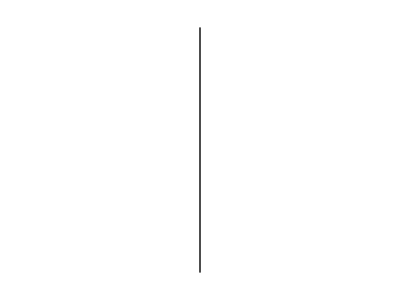

```mathematica
Graphics[
Line[{{0,1},{0,-1}}]]
```

c) Add the ball to the drawing so that it moves when its center changes (Use Dynamic).

d) Define a function `onRamp` that takes the center of the ball and returns True if the ball is on the ramp.

e) Define a function `updateVelocity` that takes the current velocity vector of the ball and angle α, and returns the new velocity as the ball moves down the ramp with slope α after time Δt.

f) Define a function `velocityToRamp` that takes the current velocity vector of the ball and angle α, and returns the new velocity as the ball transitions from the flat surface onto the ramp with slope α.

g) Define a function `updateVelocityProjectile` that takes the current velocity of the ball and returns the new velocity after time Δt during projectile motion.

h) Define a function `updatePosition` that takes the current position of the ball and its velocity, and returns the new position after time Δt.

i) Using the previous functions, simulate the motion of the ball. (4 points – motion on flat surface (1 point), motion on the ramp (1 point), projectile motion (1 point), simulation stops when the ball lands on the ground (1 point))